```mathematica
s=NDSolve[{y''[x]==-Exp[-2*y[x]],y[1]==0,y[2]==Log[2]},y[x],{x,1,2}]
```

{{y[x]→InterpolatingFunction[…][x]}}

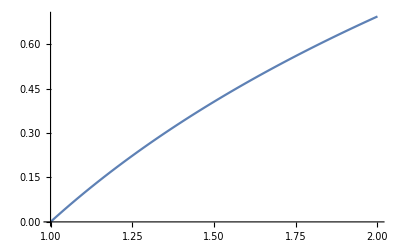

```mathematica
Plot[Evaluate[{y[x]} /.s],{x,1,2}]
```

```mathematica
s1=NDSolve[{y''[x]==y'[x]*Cos[x]-y[x]*Log[y[x]],y[0]==1,y[Pi/3]==Exp[1]},y[x],{x,0,Pi/2}]
```

{{y[x]→InterpolatingFunction[…][x]}}

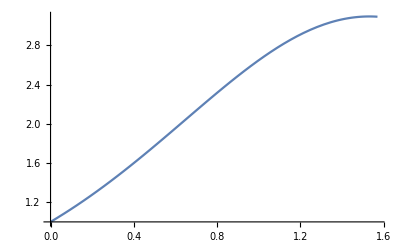

```mathematica
Plot[Evaluate[{y[x]} /.s1],{x,0,Pi/2}]
```

```mathematica
s2=NDSolve[{y''[x]==-(2*y'[x]^3+y[x]^2*y'[x]),y[Pi/4]==2^(-1/4),y[Pi/3]==12^(1/4)/2},y[x],{x,Pi/4,Pi/3}]
```

{{y[x]→InterpolatingFunction[…][x]}}

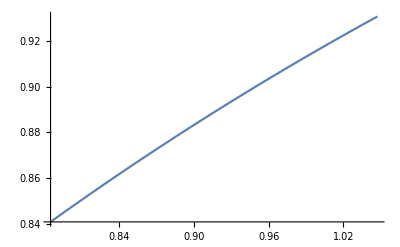

```mathematica
Plot[Evaluate[{y[x]} /.s2],{x,Pi/4,Pi/3}]
```

```mathematica
s3=NDSolve[{y''[x]==0.5-y'[x]^2/2-y[x]*Sin[x/2],y[0]==2,y[Pi]==2},y[x],{x,0,Pi}]
```